```mathematica
tuples=Tuples[{0,1},{3,3}];
```

```mathematica
tuples=Tuples[{0,1},{3,3}];

n=Length[tuples];
side=Ceiling[Sqrt[n]];

(*Rellena la lista de matrices con ceros hasta side^2,manteniendo cada bloque 3x3*)
padded=PadRight[tuples,{side^2,3,3}];

(*Acomoda los bloques en una cuadrícula side x side*)
blocks=Partition[padded,side];

(*Aplana los bloques en una sola matriz grande*)
bigMatrix=ArrayFlatten[blocks];
```

```mathematica
ArrayPlot[bigMatrix,Mesh->{Range[0,27*3,3],Range[0,27*3,3]},MeshStyle->Directive[Gray,Thick]]
```

-Graphics-

```mathematica
27*3
```

81

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["test.mat",{bigMatrix}]
```

test.mat

```mathematica
Dimensions[bigMatrix]
```

{69,69}

```mathematica
fns=FileNames["0*.mat","./"];
data=Import[#,"MAT"]&/@fns;
```

```mathematica
base=Import["../../CA/B3S23/base.mat","MAT"];
```

```mathematica
datos=AssociationMap[Import[#,"MAT"]&,fns];
```

```mathematica
centers=Flatten[Table[{i,j},{i,Range[2,69,3]},{j,Range[2,69,3]}],1];
```

```mathematica
base[[1,2]]==#&/@datos[[;;,1,2]]
```

<|./t_00001.mat→True,./t_00002.mat→True,./t_00003.mat→True,./t_00004.mat→True,./t_00005.mat→True,./t_00006.mat→True,./t_00007.mat→True,./t_00008.mat→True,./t_00009.mat→True,./t_0001.mat→True,./t_0002.mat→True,./t_0003.mat→True,./t_0004.mat→True,./t_0005.mat→True,./t_0006.mat→True,./t_0007.mat→True,./t_0008.mat→True,./t_0009.mat→True,./t_001.mat→True,./t_002.mat→True,./t_003.mat→True,./t_004.mat→True,./t_005.mat→True,./t_006.mat→True,./t_007.mat→True,./t_008.mat→True,./t_009.mat→True,./t_01.mat→True,./t_02.mat→False,./t_03.mat→False|>

```mathematica
basevector=Flatten[Part[base[[1,2]],#[[1]],#[[2]]]&/@{#}&/@centers];
```

```mathematica
vectors=Table[
Flatten[Part[i,#[[1]],#[[2]]]&/@{#}&/@centers],
{i,datos[[;;,1,2]]}
];
```

```mathematica
names=ToExpression["0."<>StringJoin[Characters[#][[4;;-5]]]]&/@Keys[datos];
```

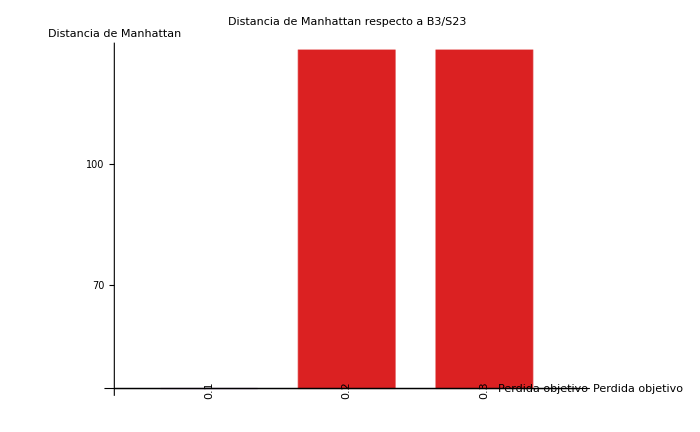

```mathematica
distancias=ManhattanDistance[basevector,#]&/@vectors;
orden=Reverse@Ordering[distancias,All,Greater];
namesSorted=names[[orden]];
distSorted=distancias[[orden]];

primerNoCero=FirstPosition[distSorted,x_/;x>0][[1]];
mask=Table[distSorted[[i]]>0||i==primerNoCero-1,{i,Length[distSorted]}];

namesFiltered=Pick[namesSorted,mask];
distFiltered=Pick[distSorted,mask];

(*Colorear según el VALOR,no según la posición*)
colorFunc=ColorData["Rainbow"];
valoresEscalados=Rescale[distFiltered]; (*normaliza entre 0 y 1*)
coloresPorValor=colorFunc/@valoresEscalados;

fplot=BarChart[distFiltered,ChartStyle->coloresPorValor,ChartLabels->Placed[Rotate[#,90 Degree]&/@namesFiltered,Axis],ScalingFunctions->"Log",AxesLabel->{"Perdida objetivo","Distancia de Manhattan"},PlotLabel->"Distancia de Manhattan respecto a B3/S23",ImageSize->700,LabelStyle->Directive[FontSize->11],BarSpacing->0.42]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./../../../../Documentation/img/b3s23_loss.png",fplot]
```

./../../../../Documentation/img/b3s23_loss.png